```mathematica
gi[x_]:= π HeavisideTheta[W-Abs[x]]/(2W)
```

```mathematica
gr[x_]:=Log[Abs[((W+x)/(W-x))]]
```

```mathematica
W=10
```

10

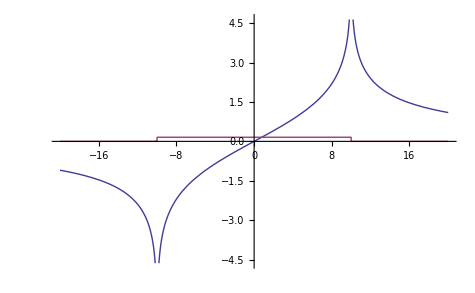

```mathematica
Plot[{gr[x],gi[x]},{x,-20,20}]
```